# Hayes & Adams (2017) Mathematica Notebook 1

## About this notebook

This document is a PDF created from a Wolfram Mathematica notebook file prepared by Mark A. Hayes during December 2016 following the general approach for matrix population analysis outlined in Ellner and Guckenheimer (2006) and used in Hayes (2011). This code and output analyzes the population matrices used in the Hayes and Adams 2017 PLOS ONE manuscript “Simulated bat populations erode when exposed to climate change projections for western North America”. This notebook is used to calculate eigenvalues and other characteristics of the matrix model used, such as sensitivity of the matrix elements to small changes in a given matrix element. The “elasticity 01022017.xlsx” spreadsheet shows sensitivity and elasticity calculations, given these eigenvalues; this notebook also shows step by step sensitivity calculations. The sensitivity and elasticity matrix plots at the end of this notebook use information from this notebook and the elasticity calculations from the spreadsheet. If you would like a copy of the original Mathematica notebook, please contact MAH at hayesm@usgs.gov or hayes.a.mark@gmail.com.  

Mark A. Hayes
January 2, 2017

```mathematica
SetDirectory[NotebookDirectory[]]
```

\\IGSKBACBFS2\groups\bts\t\mah\manuscripts\2016\Hayes & Adams 2016 - Bat pop modeling - PLOS ONE\revision - fall winter 2016\Plos One - Data package

## Definiting the parameters, matrix model, and dominant eigenvalue

```mathematica
SA=0.79;
SF=SA*0.64;
adultBirthRate=0.425;

FA=SA*adultBirthRate;
F0=0.90*adultBirthRate*SF;

m={{F0,FA,FA,FA},{SF,0,0,0},{0,SA,0,0},{0,0,SA,SA}};
MatrixForm[m]
Lambda=Eigenvalues[m,1]
```

(0.193392 | 0.33575 | 0.33575 | 0.33575
0.5056 | 0 | 0 | 0
0 | 0.79 | 0 | 0
0 | 0 | 0.79 | 0.79)

{1.00036}

```mathematica
OriginalLambda=Lambda
```

{1.00036}

```mathematica
MatrixForm[m]
```

(0.193392 | 0.33575 | 0.33575 | 0.33575
0.5056 | 0 | 0 | 0
0 | 0.79 | 0 | 0
0 | 0 | 0.79 | 0.79)

### Sensitivity of the matrix elements

Using the Ellner and Guckenheimer (2006) approach, where s is sensitivity for a given matrix element, and ∂λ is the change in lambda (λ) given a small change in the matrix element (∂a_ij). In this case we reduced each matrix element in turn by 10%, and calculated the resulting λ (dominant eigenvalue) for each change, while keeping all other elements at the original value. Thus sensitivity is the original eigenvalue minus the new eigenvalue (∂λ), divided by the change in the matrix element (∂a_ij):
s_ij=(∂λ)/(∂a_ij)

Reducing each vital rate, in turn, by 10% (Vital rate * 0.90):

Sensitivity of F0

Decreasing the matrix element by 0.10

```mathematica
0.193*0.90
```

0.1737

```mathematica
mf0 ={{0.1737,FA,FA,FA},{SF,0,0,0},{0,SA,0,0},{0,0,SA,SA}};
```

```mathematica
Eigenvalues[mf0,1]
```

{0.996351+0. ⅈ}

```mathematica
Lambdaf0=0.996351
```

0.996351

```mathematica
Sensitivityf0=(OriginalLambda-Lambdaf0)/(0.193-0.1737)
```

{0.207792}

Sensitivity of F1

```mathematica
0.336*0.9
```

0.3024

```mathematica
mf1 ={{F0,0.3024,FA,FA},{SF,0,0,0},{0,SA,0,0},{0,0,SA,SA}};
```

```mathematica
Eigenvalues[mf1,1]
```

{0.99691+0. ⅈ}

```mathematica
Lambdaf1=0.99691
```

0.99691

```mathematica
Sensitivityf1=(OriginalLambda-Lambdaf1)/(0.336-0.3024)
```

{0.10272}

Sensitivity of F2

```mathematica
0.336*0.90
```

0.3024

```mathematica
mf2 ={{F0,FA,0.3024,FA},{SF,0,0,0},{0,SA,0,0},{0,0,SA,SA}};
```

```mathematica
Eigenvalues[mf2,1]
```

{0.997622+0. ⅈ}

```mathematica
Lambdaf2=0.997622
```

0.997622

```mathematica
Sensitivityf2=(OriginalLambda-Lambdaf2)/(0.336-0.3024)
```

{0.0815294}

Sensitivity of F3+

```mathematica
0.336*0.90
```

0.3024

```mathematica
mf3  ={{F0,FA,FA,0.3024},{SF,0,0,0},{0,SA,0,0},{0,0,SA,SA}};
```

```mathematica
Eigenvalues[mf3,1]
```

{0.989689+0. ⅈ}

```mathematica
Lambdaf3=0.989689
```

0.989689

```mathematica
Sensitivityf3=(OriginalLambda-Lambdaf3)/(0.336-0.3024)
```

{0.317631}

Sensitivity of S0

```mathematica
0.506*0.90
```

0.4554

```mathematica
ms0 ={{F0,FA,FA,FA},{0.4554,0,0,0},{0,SA,0,0},{0,0,SA,SA}};
```

```mathematica
Eigenvalues[ms0,1]
```

{0.983515}

```mathematica
LambdaS0=0.983515
```

0.983515

```mathematica
SensitivityS0=(OriginalLambda-LambdaS0)/(0.506-0.4554)
```

{0.332933}

Sensitivity of S1

```mathematica
0.790*0.90
```

0.711

```mathematica
ms1 ={{F0,FA,FA,FA},{SF,0,0,0},{0,0.711,0,0},{0,0,SA,SA}};
```

```mathematica
Eigenvalues[ms1,1]
```

{0.986823}

```mathematica
LambdaS1=0.986826
```

0.986826

```mathematica
SensitivityS1=(OriginalLambda-LambdaS1)/(0.790-0.711)
```

{0.171334}

Sensitivity of S2

```mathematica
0.79*0.90
```

0.711

```mathematica
ms2 ={{F0,FA,FA,FA},{SF,0,0,0},{0,SA,0,0},{0,0,0.711,SA}};
```

```mathematica
Eigenvalues[ms2,1]
```

{0.989614+0. ⅈ}

```mathematica
LambdaS2=0.989614
```

0.989614

```mathematica
SensitivityS2=(OriginalLambda-LambdaS2)/(0.79-0.711)
```

{0.136043}

Sensitivity of S3

```mathematica
0.79*0.90
```

0.711

```mathematica
ms3 ={{F0,FA,FA,FA},{SF,0,0,0},{0,SA,0,0},{0,0,SA,0.711}};
```

```mathematica
Eigenvalues[ms3,1]
```

{0.964097+0. ⅈ}

```mathematica
LambdaS3=0.964097
```

0.964097

```mathematica
SensitivityS3=(OriginalLambda-LambdaS3)/(0.79-0.711)
```

{0.459043}

### Sensitivity Results, shown in matrix form

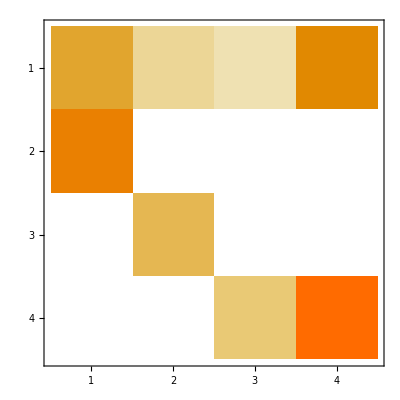

```mathematica
MatrixPlot[{{0.20779,0.1027,0.0815,0.318},{0.3329,0,0,0},{0,0.1713,0,0},{0,0,0.1360,0.4590 }}]
```

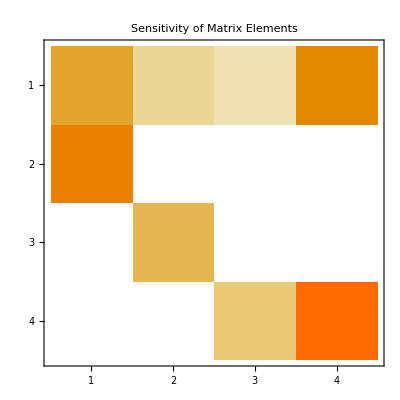

```mathematica
Show[%61,PlotLabel->HoldForm[Sensitivity of Matrix Elements],LabelStyle->{13,GrayLevel[0]}]
```

### Elasticity matrix

See calculations in “elasticity 01022017.xlsx” excel spreadsheet

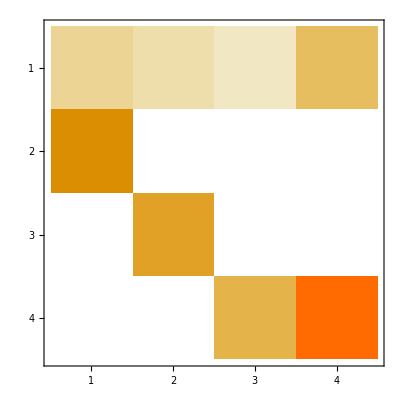

```mathematica
MatrixPlot[{{0.040075,0.0344875,0.02737,0.1066716},{0.16838,0,0,0},{0,0.13529,0,0},{0,0,0.10742,0.3624995 }}]
```

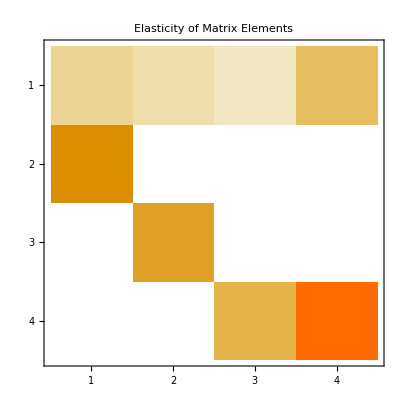

```mathematica
Show[%17,PlotLabel->HoldForm[Elasticity of Matrix Elements],LabelStyle->{13,GrayLevel[0]}]
```